```mathematica
Clear[DPlot];
DPlot[eqn_,u_,x_,fic_,sic_,dom_,codom_:{},n_:10,epilogValues_:{},styles_:{}]:=Module[{i,j,eqs,fics,sics,temp,temp2,ics,plots},
eqs={};
fics={};
sics={};
temp={};
temp2={};
ics={};
plots={};
If[Length[fic]!=0,
If[TrueQ[fic[[1,0]]==List],
For[i =0,i<Length[fic],i++,
temp=Subdivide[fic[[i+1,2]],fic[[i+1,3]],n];
For[j=0,j<n+1,j++,
AppendTo[temp2,fic[[i+1,1]]==temp[[j+1]]];
];
AppendTo[fics,temp2];
temp2={};
];
,(*else*)
temp=Subdivide[fic[[2]],fic[[3]],n];
For[j=0,j<n+1,j++,
AppendTo[temp2,fic[[1]]==temp[[j+1]]];
];
AppendTo[fics,temp2];
temp2={};
];
];
If[Length[sic]!=0,
If[TrueQ[sic[[1,0]]==List],
For[i=0,i<Length[sic],i++,
temp=Subdivide[sic[[i+1,2]],sic[[i+1,3]],n];
For[j=0,j<n+1,j++,
AppendTo[temp2,sic[[i+1,1]]==temp[[j+1]]];
];
AppendTo[sics,temp2];
temp2={};
];
,(*else*)temp=Subdivide[sic[[2]],sic[[3]],n];
For[j=0,j<n+1,j++,
AppendTo[temp2,sic[[1]]==temp[[j+1]]];
];
AppendTo[sics,temp2];
temp2={};
];
];
temp={};
If[Length[fics]!=0,
For[i=0,i<n+1,i++,
For[j=0,j<Length[fics],j++,
AppendTo[temp,fics[[j+1,i+1]]];
];
For[j=0,j<Length[sics],j++,
AppendTo[temp,sics[[j+1,i+1]]];
];
AppendTo[ics,temp];
temp={}
];
];
For[i=0,i<Length[ics],i++,
If[TrueQ[ics[[1,0]]==List],
For[j=0,j<Length[ics[[i+1]]],j++,
temp=DSolve[{eqn,ics[[i+1]]},u,x][[All,1,2]];
AppendTo[eqs,temp];
];
,(*else*)
temp=DSolve[{eqn,ics[[i+1]]},u,x][[All,1,2]];
AppendTo[eqs,temp];
];
];
For[i=0,i<Length[eqs],i++,
If[TrueQ[codom=={}],
AppendTo[plots,Plot[eqs[[i+1,1]],{x,dom[[1]],dom[[2]]},Epilog->epilogValues,PlotStyle->styles]];
,(*else*)
AppendTo[plots,Plot[eqs[[i+1,1]],{x,dom[[1]],dom[[2]]},PlotRange->codom,Epilog->epilogValues,PlotStyle->styles]];
];
];
Return[Show[plots]];
]
```

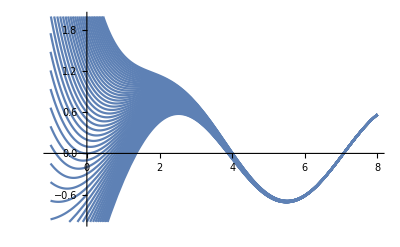

```mathematica
DPlot[y'[x]+y[x]==Sin[x],y[x],x,{y[0],-2,3},{},{-1,8},{-1,2},50]
```

```mathematica
Clear[DStreamPlot];
DStreamPlot[eqn_,u_,x_,dom_,codom_:{},res_:7]:=Module[{i,j,plots,xVals,localX,ics,epilogPoints,temp},
plots={};
ics={};
xVals=Subdivide[dom[[1]],dom[[2]],res];
epilogPoints={};
For[i=0,i<Length[xVals],i++,
AppendTo[epilogPoints,ColorData[97,"ColorList"][[Mod[i,15]+1]]];
temp=Subdivide[codom[[1]],codom[[2]],res];
For[j=0,j<res+1,j++,
AppendTo[epilogPoints,Point[{xVals[[i+1]],temp[[j+1]]}]];
];
];
For[i=0,i<Length[xVals],i++,
AppendTo[ics,{u/.x->xVals[[i+1]],codom[[1]],codom[[2]]}];
];
For[i=0,i<Length[ics],i++,
AppendTo[plots,DPlot[eqn,u,x,ics[[i+1]],{},dom,codom,res,{PointSize[Large],epilogPoints},{ColorData[97,"ColorList"][[Mod[i,15]+1]]}]];
];
Return[Show[plots]];
];
```

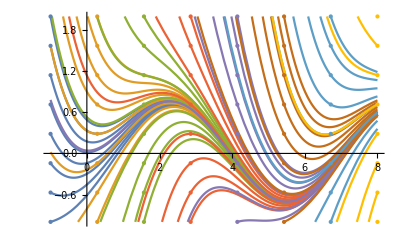

```mathematica
DStreamPlot[y'[x]+y[x]==Sin[x],y[x],x,{-1,8},{-1,2},7]
```